v2: updated version following notes, plus Mean-field
v3: mean-field (more) + ϵ implementation, bsp

v4: mean-field corrected

v5: mean-field zero solutions
v5-check: check why zero solutions
v5-ch-mu: do MF at a fixed μ
v6: follow notes
v7: clean-up, ZA: n vs μ
v7c: clean notebook

### Set Options

Automating good looking plots

```mathematica
SetOptions[ DiscretePlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
SetOptions[ ListPlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium,PlotStyle->{Black,Thick}];
```

```mathematica
SetOptions[ ListContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ ListDensityPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
```

```mathematica
SetOptions[ ContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ DensityPlot,Frame-> True,LabelStyle->{FontFamily->"CMU Serif",FontSize->24,Black},ImageSize->Medium];
```

### Parameters

Lattice vectors, and basis vectors

```mathematica
a1 = {1,0};a2 ={0,1};τA = {1/2,0};τB = {0,0}; τC = {0,1/2};τvec = {τA,τB, τC};
```

Reciprocal lattice vectors

```mathematica
LatMat = {a1,a2}; 
ReciLatMat = 2π Inverse[LatMat]†;
b1 = ReciLatMat[[1]] ;b2 = ReciLatMat[[2]];
```

```mathematica
δf=N[1/(2√2)];
```

kSpan : set of points for k-sums, and rSpan : set of points for r-sums

```mathematica
kSpan[krange_]:=N[Flatten[Table[i*b1+j*b2,{i,0,0.999,1/krange},{j,0,0.999,1/krange}],1]];
```

```mathematica
rSpan[range_]:=N[Flatten[Table[i*a1+j*a2,{i,-range,range},{j,-range,range}],1]];
```

```mathematica
inp[a_,b_]:= Conjugate[a].b;
```

We will play around with k-range and range to check for convergence

```mathematica
Fermi[β_,x_]:=Chop[N[ 1/(1+ Exp[ β x])]];DFermi[β_,x_] :=D[ Fermi[β,x1],x1]/.{x1-> x};
```

### Bloch Hamiltonian

```mathematica
MatX[λ_,δ_,k_] := Module[ {λR = λ[[1]], λD = λ[[2]],δx = δ[[1]], δy = δ[[2]]}, (1+δx)(IdentityMatrix[2]+ I λR PauliMatrix[2] +I λD PauliMatrix[1]) + (1-δx)Exp[I k.a1](IdentityMatrix[2]- I λR PauliMatrix[2] -I λD PauliMatrix[1])];
```

```mathematica
MatY[λ_,δ_,k_] := Module[ {λR = λ[[1]], λD = λ[[2]],δx = δ[[1]], δy = δ[[2]]}, (1+δy)(IdentityMatrix[2]- I λR PauliMatrix[1] +I λD PauliMatrix[2]) + (1-δy)Exp[I k.a2](IdentityMatrix[2]+ I λR PauliMatrix[1] -I λD PauliMatrix[2])];
```

```mathematica
Clear[hamLieb];hamLieb[bsp_,k_] := hamLieb[bsp,k] = Module[{λ = bsp[[1]], δ = bsp[[2]], ϵ = bsp[[3]]},Module[ {mx = MatX[λ,δ,k],my = MatY[λ,δ,k] },ArrayFlatten[ {{-ϵ IdentityMatrix[2],mx,my},{mx†,0,0},{my†,0,0}} ]]];
```

```mathematica
Clear[EnerLieb];EnerLieb[bsp_,k_] := EnerLieb[bsp,k]= Chop[  N[Sort[Eigenvalues[hamLieb[bsp,k] ]]] ];
Clear[ULieb];ULieb[bsp_,k_] :=ULieb[bsp,k]=Transpose[Chop[N[   Transpose[ SortBy[ Transpose[ Eigensystem[ hamLieb[bsp,k] ] ] ,First ] ][[2]] ] ] ] ;
```

#### Plot Band Structure

```mathematica
Gama = {0,0}; Xpoint = b1/2; Mpoint = 1/2(b1+b2);
```

```mathematica
BetAB[ a_, b_] = Table[ (1-i)*a +i*b , {i,0.,1,0.01}];
```

```mathematica
kCut = Join[BetAB[ Gama,Xpoint]  ,BetAB[Xpoint,Mpoint], BetAB[Mpoint,Gama] ];
```

```mathematica
PlotDispData[bsp_] := Table[ EnerLieb[bsp,k]  ,{k,kCut} ];
```

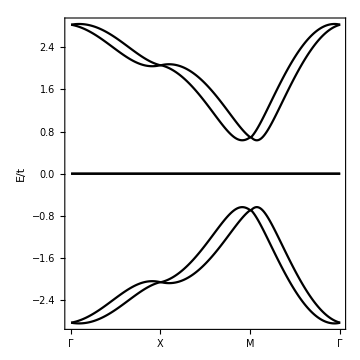

```mathematica
Block[ {bsp={{0.1,0.1},{0.2,0.2},0.0}},ListPlot[Table[ PlotDispData[bsp][[All,i]],{i,1,6}],PlotStyle->Black,
FrameTicks->{{{1,"Γ"},{101,"X"},{202,"M"},{303,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"E/t"},AspectRatio->1/1]]
```

```mathematica
Block[{bsp={{0.45,0.0},{0.0,0.0},0.0},k=RandomReal[1,2]}, EnerLieb[bsp,k]]
```

{-2.93116,-2.6731,0,0,2.6731,2.93116}

### Mean Field Theory

#### Mean-Field self-consistent set up

Here nup, ndn, splus and sdown are all 3 vectors (for A, B, C)

```mathematica
IJMat[i_,j_]:= ArrayFlatten[ Table[ If[i1==i&&j1==j,1,0],{i1,1,6},{j1,1,6}]];
```

MF vec = { n_(A↑), n_(A↓), n_(B↑),  n_(B↓), n_(C↑),n_(C↓), (S^+)_A, (S^+)_B, (S^+)_C}

```mathematica
MvMat = {IJMat[1,1],IJMat[2,2],IJMat[3,3],IJMat[4,4],IJMat[5,5],IJMat[6,6],IJMat[1,2],IJMat[3,4],IJMat[5,6]};
```

```mathematica
MFHamvec = {IJMat[2,2],IJMat[1,1],IJMat[4,4],IJMat[3,3],IJMat[6,6],IJMat[5,5],-IJMat[2,1],-IJMat[4,3],-IJMat[6,5]};
```

```mathematica
Clear[HamMFU];HamMFU[MFvec_]:= HamMFU[MFvec] =MFvec[[1;;6]].MFHamvec[[1;;6]] +MFvec[[7;;9]].MFHamvec[[7;;9]]+(MFvec[[7;;9]].MFHamvec[[7;;9]])†;
```

```mathematica
Clear[HamMFull];HamMFull[bsp_,MFvec_,k_,U_,μ_]:= HamMFull[bsp,MFvec,k,U,μ]= hamLieb[bsp,k] +U HamMFU[MFvec]- (μ+U/2)IdentityMatrix[6];
```

```mathematica
HamMFull[{{0.0,0.0},{0.2,0.2},0.0},{nAu, nAd, nBu, nBd, nCu, nCd, SpA, SpB, SpC},Gama,U,μ]//MatrixForm
```

(0.-U/2+nAd U-μ | 0.-U Conjugate[SpA] | 2.+0. ⅈ | 0.+0. ⅈ | 2.+0. ⅈ | 0.+0. ⅈ
0.-SpA U | 0.-U/2+nAu U-μ | 0.+0. ⅈ | 2.+0. ⅈ | 0.+0. ⅈ | 2.+0. ⅈ
2.+0. ⅈ | 0.+0. ⅈ | -U/2+nBd U-μ | -U Conjugate[SpB] | 0 | 0
0.+0. ⅈ | 2.+0. ⅈ | -SpB U | -U/2+nBu U-μ | 0 | 0
2.+0. ⅈ | 0.+0. ⅈ | 0 | 0 | -U/2+nCd U-μ | -U Conjugate[SpC]
0.+0. ⅈ | 2.+0. ⅈ | 0 | 0 | -SpC U | -U/2+nCu U-μ)

```mathematica
Clear[EnerMF];EnerMF[bsp_,MFvec_,k_,U_,μ_] := EnerMF[bsp,MFvec,k,U,μ]= Chop[  N[Sort[Eigenvalues[HamMFull[bsp,MFvec,k,U,μ] ]]] ];
```

```mathematica
Clear[ULiebMF];ULiebMF[bsp_,MFvec_,k_,U_,μ_] :=ULiebMF[bsp,MFvec,k,U,μ]=Transpose[Transpose[SortBy[Transpose[Eigensystem[ HamMFull[bsp,MFvec,k,U,μ]]],First]][[2]]]
```

```mathematica
Clear[MFvalue];MFvalue[bsp_,MFvec_,U_,μ_,β_,krange_] :=MFvalue[bsp,MFvec,U,μ,β,krange]=Table[1/Length[kSpan[krange]] Chop[Sum[ Module[{um = ULiebMF[bsp,MFvec,k,U,μ]}, Fermi[β, EnerMF[bsp,MFvec,k,U,μ][[band]] ](um†.MvMat[[mfvectors]].um)[[band,band]]],{band,1 ,6},{k,kSpan[krange]}]],{mfvectors,1,9}];
```

Take the initial seed from the U → ∞ limit

```mathematica
InitSeed = Table[ 0.5, {i,1,9}];
```

```mathematica
Clear[MFsoln];MFsoln[bsp_,U_,μ_,β_,krange_]:= MFsoln[bsp,U,μ,β,krange]=MFvec/.FindRoot[ MFvec - MFvalue[bsp,MFvec,U,μ,β,krange],{MFvec,InitSeed},Evaluated->False,MaxIterations->10,PrecisionGoal->3,AccuracyGoal->3]
```

```mathematica
Clear[NumEq];NumEq[MFvec_] :=NumEq[MFvec]=Total[ MFvec[[1;;6]] ];
```

### Half-filling, μ=0

```mathematica
Clear[MagnHF];MagnHF[bsp_,U_, β_,krange_,orb_]:=  MagnHF[bsp,U,β,krange,orb]=Module[{itrMF=MFsoln[bsp,U,0.0,β,krange]},{Re[itrMF[[orb+6]]] ,Im[itrMF[[orb+6]]], 1/2( itrMF[[orb+3]] - itrMF[[orb]])}];
```

### Export files

```mathematica
dataHF = Block[ {bsp={{0.0,0.0},{0.2,0.2},0.0}, β=100, krange=30},Table[ArrayFlatten[{ U,MFsoln[bsp,U,0.0,β,krange]},1], {U,0.0,10.0}]];
```

```mathematica
Export["/home/verma.148/fbint/dataHF.txt",dataHF];
```

```mathematica
dataU0p2mu = Block[ {bsp={{0.0,0.0},{0.2,0.2},0.0},U=0.2, β=100, krange=30},Table[ArrayFlatten[{ μ,MFsoln[bsp,U,μ,β,krange]},1], {μ,-0.1,0.1,0.01}]];
```

```mathematica
Export["/home/verma.148/fbint/dataU0p2mu.txt",dataU0p2mu];
```

```mathematica
dataU2p0mu = Block[ {bsp={{0.0,0.0},{0.2,0.2},0.0},U=2.0, β=100, krange=30},Table[ArrayFlatten[{ μ,MFsoln[bsp,U,μ,β,krange]},1], {μ,-0.1,0.1,0.01}]];
```

```mathematica
Export["/home/verma.148/fbint/dataU2p0mu.txt",dataU2p0mu];
```